# NV-Centre ESR simulation

```mathematica
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];
```

## Initialisation

## NV-Centre constants

```mathematica
γN = 19.331*10^6; (* Gyromagnetic ratio for^14 N [s^-1 T^-1] *)
γe = 1.7609*10^11; (* Gyromagnetic ratio for e- [rad s^-1 T^-1] *)
B0 =0*513 *10^-4 (* DC Applied field [T] *);
ωs= (-γe B0)/(2π); (* [Hz] *)
ωI=(γN B0)/(2π); (* [Hz] *)
Ahf = -2.16*10^6 ; (* Hyperfine interaction [Hz] *)
Dzfs = 2870*10^6 ; (* Zero-field-splitting for electron triplet [Hz] *)
Pzfs = -4.95*10^6 ; (* Zero-field-splitting for^14 N [Hz] *)

Axyhf = -2.1*10^6;
Azhf = -2.16*10^6 ; (* Hyperfine interaction [Hz] *)
```

## Operators

```mathematica
(* Triplet spin operators *)

Sx = 1/Sqrt[2]{ {  0, 1, 0} , { 1, 0, 1}, {0, 1, 0 } };
Sy = 1/(Sqrt[2] I){ {  0, -1, 0} , { 1, 0, 1}, {0, -1, 0 } };
Sy = {{0,-ⅈ/(√2),0},{ⅈ/(√2),0,-ⅈ/(√2)},{0,ⅈ/(√2),0}};
Sz = { {1, 0, 0 }, {0, 0, 0}, {0, 0, -1}};
eye = IdentityMatrix[3];

(* Electron triplet operators *)

eSx = KroneckerProduct[Sx, eye];
eSy = KroneckerProduct[Sy, eye];
eSz = KroneckerProduct[Sz, eye];

(* Nuclear operators *)

Ix = KroneckerProduct[eye, Sx];
Iy = KroneckerProduct[eye, Sy];
Iz = KroneckerProduct[eye, Sz];
```

## Hamiltonian

Hhf is the hyperfine interaction.
Hnv is the Hamiltonian of the NV-centre.
Hc is the time-dependent perturbation on the Hamiltonian.
H is the complete Hamiltonian.
.1a

```mathematica
Hhf=  Ahf eSz . Iz; (* Secular approximation *)
Hhf= ( Axyhf( eSx.Ix + eSy.Iy ) + Azhf eSz . Iz); 
Hnv = ( Dzfs eSz.eSz  + ωs eSz + Pzfs  Iz.Iz - ωI Iz) + Hhf;
Hc[t_]:= pulseAmplitude  KroneckerProduct[Sx, Sx] Sin[ 2π pulseFreq t + pulsePhase ]  ;
H[t_] := Hnv+ Hc[t]

systemSize = Length[H[0]];
```

```mathematica
Hnv // MatrixForm
```

(2.86289×10^9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 2.87×10^9 | 0. | -2.1×10^6 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 2.86721×10^9 | 0. | -2.1×10^6 | 0. | 0. | 0. | 0.
0. | -2.1×10^6 | 0. | -4.95×10^6 | 0. | 0. | 0. | 0. | 0.
0. | 0. | -2.1×10^6 | 0. | 0. | 0. | -2.1×10^6 | 0. | 0.
0. | 0. | 0. | 0. | 0. | -4.95×10^6 | 0. | -2.1×10^6 | 0.
0. | 0. | 0. | 0. | -2.1×10^6 | 0. | 2.86721×10^9 | 0. | 0.
0. | 0. | 0. | 0. | 0. | -2.1×10^6 | 0. | 2.87×10^9 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.86289×10^9)

## Density matrix

```mathematica
density = Table[ ρ[i, j][t],{i, 1, systemSize}, {j, 1, systemSize}] ;
Do[
density[[j, i]] = Conjugate[density[[i,j]]];
, {i, 1, systemSize}, {j, i+1, systemSize}];

density // MatrixForm
```

(ρ[1,1][t] | ρ[1,2][t] | ρ[1,3][t] | ρ[1,4][t] | ρ[1,5][t] | ρ[1,6][t] | ρ[1,7][t] | ρ[1,8][t] | ρ[1,9][t]
Conjugate[ρ[1,2][t]] | ρ[2,2][t] | ρ[2,3][t] | ρ[2,4][t] | ρ[2,5][t] | ρ[2,6][t] | ρ[2,7][t] | ρ[2,8][t] | ρ[2,9][t]
Conjugate[ρ[1,3][t]] | Conjugate[ρ[2,3][t]] | ρ[3,3][t] | ρ[3,4][t] | ρ[3,5][t] | ρ[3,6][t] | ρ[3,7][t] | ρ[3,8][t] | ρ[3,9][t]
Conjugate[ρ[1,4][t]] | Conjugate[ρ[2,4][t]] | Conjugate[ρ[3,4][t]] | ρ[4,4][t] | ρ[4,5][t] | ρ[4,6][t] | ρ[4,7][t] | ρ[4,8][t] | ρ[4,9][t]
Conjugate[ρ[1,5][t]] | Conjugate[ρ[2,5][t]] | Conjugate[ρ[3,5][t]] | Conjugate[ρ[4,5][t]] | ρ[5,5][t] | ρ[5,6][t] | ρ[5,7][t] | ρ[5,8][t] | ρ[5,9][t]
Conjugate[ρ[1,6][t]] | Conjugate[ρ[2,6][t]] | Conjugate[ρ[3,6][t]] | Conjugate[ρ[4,6][t]] | Conjugate[ρ[5,6][t]] | ρ[6,6][t] | ρ[6,7][t] | ρ[6,8][t] | ρ[6,9][t]
Conjugate[ρ[1,7][t]] | Conjugate[ρ[2,7][t]] | Conjugate[ρ[3,7][t]] | Conjugate[ρ[4,7][t]] | Conjugate[ρ[5,7][t]] | Conjugate[ρ[6,7][t]] | ρ[7,7][t] | ρ[7,8][t] | ρ[7,9][t]
Conjugate[ρ[1,8][t]] | Conjugate[ρ[2,8][t]] | Conjugate[ρ[3,8][t]] | Conjugate[ρ[4,8][t]] | Conjugate[ρ[5,8][t]] | Conjugate[ρ[6,8][t]] | Conjugate[ρ[7,8][t]] | ρ[8,8][t] | ρ[8,9][t]
Conjugate[ρ[1,9][t]] | Conjugate[ρ[2,9][t]] | Conjugate[ρ[3,9][t]] | Conjugate[ρ[4,9][t]] | Conjugate[ρ[5,9][t]] | Conjugate[ρ[6,9][t]] | Conjugate[ρ[7,9][t]] | Conjugate[ρ[8,9][t]] | ρ[9,9][t])

## Master equation

```mathematica
eqnTotal = ⅈ  D[ density, t] - (H[t].density - density.H[t]) // Simplify;

eqns = Table[ eqnTotal[[i, j]],  {i, 1, systemSize}, {j, i, systemSize}] // Flatten;
diffeqs = Table[ eqns[[i]] == 0, {i, 1, Length[eqns]}];
funcs =Table[ density[[i, j]],  {i, 1, systemSize}, {j, i, systemSize}] // Flatten;
initialStateEqs =  Table[ ρ[i, j][0] == density0[[i, j]],  {i, 1, systemSize}, {j, i, systemSize}]  // Flatten;
params = { diffeqs, initialStateEqs } // Flatten;
```

## Functions

For a density matrix ρ in the space A_1 ⊗ A_2 ⊗ ... ⊗ A_n, the function will return the reduced density matrix ρ_A_1.

```mathematica
GetSubsystemA[density_, subSystemSize_] := Map[ Tr, Partition[ density, {Length[density]/subSystemSize, Length[density]/subSystemSize}], {2}];
```

Set the variable comments to the desired message to be put inside the data output of the simulation.

```mathematica
comments = StringRiffle[{
"Pulse that acts on both nuclear spin and electron spin",
StringForm["B0=``T",B0],
StringForm["Frequency Resolution=``Hz", pulseFreqStep],
StringForm["Pulse amplitude=``Hz", pulseAmplitude]
}, ". "];
Print[comments];
```

Pulse that acts on both nuclear spin and electron spin. B0=0T. Frequency Resolution=pulseFreqStepHz. Pulse amplitude=pulseAmplitudeHz

Set the file-name for the output

```mathematica
fileName = "results/nv_center_esr"  <> StringReplace[ DateString["ISODateTime"], ":" -> "."];
```

## Simulation parameters

```mathematica
pulseAmplitude = 7*10^6; (* [Hz] *)
pulsePhase = 0; (* [Rad] *)

tStart = 0; (* [s] *)
tEnd = 2*10^-6; (* [s] *)

(*
pulseFreqStart = 500*10^6; (* [Hz] *)
pulseFreqEnd = 530*10^7; (* [Hz] *) 
pulseFreqStart = 1.369*10^9;
pulseFreqEnd=1.5*10^9;
pulseFreqStart = 1.43*10^9;
pulseFreqEnd=1.4331*10^9;
pulseFreqStart = 7.16*10^9; (* [Hz] *)
pulseFreqEnd = 7.22*10^8; (* [Hz] *) *)

pulseFreqStart = 2.867*10^9; (* [Hz] *)
pulseFreqEnd = 2.881*10^9; (* [Hz] *) 
pulseFreqStep = 10^6; (* [Hz] *) 
calculations = Table[ f, {f, pulseFreqStart, pulseFreqEnd, pulseFreqStep}] // Length ;
```

### Initial state of the system

```mathematica
es = Eigensystem[Hnv];
groundState = {es[[2]][[Position[es[[1]], Min[es[[1]]]][[1]][[1]]]]} // Transpose;
density0 = groundState . ConjugateTranspose[groundState] ;
```

```mathematica
density0  // MatrixForm
```

(0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.999999 | 0. | 0.000730447 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.000730447 | 0. | 5.33553×10^-7 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.)

## Perform simulation

```mathematica
data = {}; (* Store T0 probability data for each frequency *)
spin0vec = { {0}, {1}, {0} };
tic=AbsoluteTime[];
count = 1;
```

{{ρ[4,4][t]+ρ[5,5][t]+ρ[6,6][t]}}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.03094×10^-7}. NIntegrate obtained 1.98551×10^-6-5.0828×10^-26 ⅈ and 2.69142×10^-12 for the integral and error estimates.

$Aborted

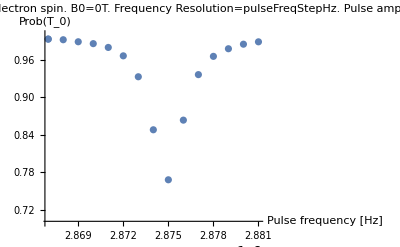

Total time taken (min) = 20.15082

```mathematica
Do[
sol = NDSolve[ params /. pulseFreq -> f, funcs, {t, tStart, tEnd}, 
PrecisionGoal->7,AccuracyGoal->7, MaxSteps->Infinity];
(*, 
PrecisionGoal->7,AccuracyGoal->7,Method->{"StiffnessSwitching"},MaxSteps->Infinity*)

(* Take electron triplet sybsystem of state*)

pFunc = ConjugateTranspose[spin0vec] . GetSubsystemA[density, 3] . spin0vec;

p = 1/(tEnd - tStart)NIntegrate[pFunc[[1]][[1]] /. sol, {t, tStart, tEnd}];
AppendTo[data, {f, p[[1]]}];

NotebookDelete[prw];
prw = PrintTemporary["Calculation ", count, " out of ", calculations];
count = count + 1;

, {f, pulseFreqStart, pulseFreqEnd, pulseFreqStep}];

toc=AbsoluteTime[];
ttot = N[(toc-tic)/60];

freqAxis = Table[f, {f, pulseFreqStart, pulseFreqEnd, pulseFreqStep}];
plot = ListPlot[data, PlotLabel->Style[comments, 12], AxesLabel -> { "Pulse frequency [Hz]", "Prob(T_0)"}, PlotRange->{0.7, 1}, ImageSize->Full ]
Print["Total time taken (min) = ",ttot,2]
```

## Save simulation data

```mathematica
Export[fileName<> "_data.csv", data];
Export[fileName<> "_plot.pdf", plot];
Save[ fileName <> "_params.dat", {  comments, ttot, pulseAmplitude,pulsePhase,pulseFreqStart,pulseFreqEnd,calculations,pulseFreqStep,γN,γe,B0,ωs,ωI,Ahf,Dzfs,Pzfs, eSx, eSz, Iz, Hhf, Hnv, Hcop}];
```

## Run simulations

## Environment parameters